```mathematica
Needs["ErrorBarPlots`"]
```

```mathematica
DiMauro={{0.11592770333719869 ,1.430902724036737*10^-7 },{0.1552419727919801,1.3179420496721543*10^-7},{0.20454943547538015,8.583697005721025*10^-8},{0.2761483125230999,9.429532155412788*10^-8},{0.36803607894880785,1.5174694782872762*10^-7},{0.48679704343252744,2.3027136175334634*10^-7},{0.6526663609063482,2.762615710198307*10^-7},{0.868657027321059,3.2949591880051146*10^-7},{1.164235975134054,3.6624168819479853*10^-7},{1.5487794318504893,3.9298828318905065*10^-7},{2.073515175360936,3.4332619284070296*10^-7},{2.756110370684767,3.0707058382385326*10^-7},{3.6645869109432856,2.9470080134723354*10^-7},{4.938211547069397,2.15863437995542*10^-7},{6.609896317259527,1.7992791265356413*10^-7},{8.653956168958699,1.4393323808133127*10^-7},{11.585659239935609,1.250078960579582*10^-7},{15.282166070975402,1.0358715668866392*10^-7},{20.457126458496873,8.787762697302056*10^-8},{27.388854044575474,7.722477322409351*10^-8},{36.36344700262212,5.3653189668710636*10^-8},{48.734279516882474,5.8940160269446834*10^-8},{65.21964092744737,4.714914987619674*10^-8},{86.75685271001828,5.000157918665334*10^-8}};
Zhong12={{0.2698936461850911,2.0235896477251556*10^-8},{0.4031852049908963,5.55773658648687*10^-8},{0.5306041497635453,8.286427728546843*10^-8},{0.6836949708649847,9.319395762340776*10^-8},{0.8809558187480787,7.722449945836255*10^-8},{1.1593649950439693,1.2067926406393264*10^-7},{1.493866975713819,1.2949258422052604*10^-7},{1.965974958149487,1.52641796717523*10^-7},{2.5332014314857654,1.4563484775012414*10^-7},{3.3337711183217964,1.5627069765469932*10^-7},{4.205844492778353,1.4563484775012414*10^-7},{7.284258025108297,8.68511373751352*10^-8},{51.951289318465555;3.23745754281764*10^-8}};
(*Calore={{{0.3204486923217852,6.9564960995706185*10^-9},ErrorBar[1.2648552168552983*10^-7,5.261243901795341*10^-9]},{{0.3759635927148633,5.6521774773949544*10^-8},ErrorBar[1.67683293681101*10^-7,4.291934260128787*10^-8]},{{0.41753189365604004,5.870937850692427*10^-8},ErrorBar[1.7575106248547964*10^-7,4.641588833612791*10^-8]},{{0.4605597747647078,7.425886368281534*10^-8},ErrorBar[1.9006912028137782*10^-7,5.779692884153325*10^-8]},{{0.5224596297751556,8.28642772854686*10^-8},ErrorBar[(*3.556480306223136*10^-7*) 1.9006912028137782*10^-7,6.551285568595522*10^-8]},{{0.5844323938042159,2.0879874845047515*10^-7},ErrorBar[3.288567819970276*10^-7,8.96150501946605*10^-8]},{{0.6556985133819497,2.5967438685878555*10^-7},ErrorBar[3.7275937203149455*10^-7,1.3051074191219142*10^-7]},{{0.7475885795969246,2.0574088705192087*10^-7},ErrorBar[3.1871416115850785*10^-7,9.691579392800516*10^-8]},{{0.8531678524172814,2.9935772947204905*10^-7},ErrorBar[4.0949150623804273*10^-7,1.7575106248547964*10^-7]},{{0.9855215688383892,2.9648599685278553*10^-7},ErrorBar[4.0949150623804273*10^-7,4.498432668969453*10^-7]},{{1.1387901130668405,3.4600097472326136*10^-7},ErrorBar[4.498432668969453*10^-7,2.1884471064600369*10^-7]},{{1.3317708758407547,3.6002561319062116*10^-7},ErrorBar[4.5694501687891855*10^-7,2.641001862504401*10^-7]},{{1.6149512770943755,3.2538091209159305*10^-7},ErrorBar[4.1595621630718514*10^-7,2.3667351447252376*10^-7]},{{1.9291989145345407,3.9859764927376447*10^-7},ErrorBar[4.789300737773289*10^-7,3.0888435964774847*10^-7]},{{2.2947423401149027,3.541113510035906*10^-7},ErrorBar[4.498432668969453*10^-7,2.768068739417855*10^-7]},{{2.926352575600284,3.3897972273636966*10^-7},ErrorBar[4.225229858223504*10^-7,2.599955928668555*10^-7]},{{3.737141937450008,3.316333172539281*10^-7},ErrorBar[3.968619443383451*10^-7,2.6826957952797275*10^-7]},{{5.094806239666136,2.909218779465988*10^-7},ErrorBar[3.556480306223136*10^-7,2.329951810515372*10^-7]},{{7.157154694129966,1.7752688336350715*10^-7},ErrorBar[2.2580912953008987*10^-7,1.2848236951554498*10^-7]},{{10.018497226843353,2.1426863106901705*10^-7},ErrorBar[2.641001862504401*10^-7,1.574994028640114*10^-7]},{{15.794220821098424,1.0308061514091419*10^-7},ErrorBar[1.5026946780037864*10^-7,5.779692884153325*10^-8]},{{28.193766915612823,9.411434162314103*10^-8},ErrorBar[1.2451970847350344*10^-7,6.153407071116611*10^-8]},{{62.79922353366887,5.360538616292313*10^-8},ErrorBar[8.030857221391537*10^-8,2.188447106460037*10^-8]}};*)
Zhong1={{0.2756556969794437;2.5595479226995333*10^-8},{0.41179294238496555;7.906043210907701*10^-8},{0.5306041497635453;1.2648552168552957*10^-7},{0.6836949708649847;1.5998587196060571*10^-7},{0.8809558187480787;1.389495494373136*10^-7},{1.1593649950439693;1.8420699693267125*10^-7},{1.525760047357919;1.8858632787726476*10^-7},{1.965974958149487;1.9765980717016307*10^-7},{2.5332014314857654;1.7575106248547896*10^-7},{3.3337711183217964;1.8858632787726476*10^-7},{4.295636490267305;1.7992936232915516*10^-7},{7.439772114947442;1.0730309405261565*10^-7},{51.951289318465555;3.906939937054621*10^-8}};
```

```mathematica
(*Let's create a matrix with error bars!*)
Clear[Calore];
Calore={{0.3204486923217852,6.9564960995706185*10^-9},{0.3759635927148633,5.6521774773949544*10^-8},{0.41753189365604004,5.870937850692427*10^-8},{0.4605597747647078,7.425886368281534*10^-8},{0.5224596297751556,8.28642772854686*10^-8},{0.5844323938042159,2.0879874845047515*10^-7},{0.6556985133819497,2.5967438685878555*10^-7},{0.7475885795969246,2.0574088705192087*10^-7},{0.8531678524172814,2.9935772947204905*10^-7},{0.9855215688383892,2.9648599685278553*10^-7},{1.1387901130668405,3.4600097472326136*10^-7},{1.3317708758407547,3.6002561319062116*10^-7},{1.6149512770943755,3.2538091209159305*10^-7},{1.9291989145345407,3.9859764927376447*10^-7},{2.2947423401149027,3.541113510035906*10^-7},{2.926352575600284,3.3897972273636966*10^-7},{3.737141937450008,3.316333172539281*10^-7},{5.094806239666136,2.909218779465988*10^-7},{7.157154694129966,1.7752688336350715*10^-7},{10.018497226843353,2.1426863106901705*10^-7},{15.794220821098424,1.0308061514091419*10^-7},{28.193766915612823,9.411434162314103*10^-8},{62.79922353366887,5.360538616292313*10^-8}};
CaloreYBars={{5.261243901795341*10^-9,1.2451970847350344*10^-7},{4.3596917354484804*10^-8,1.7033053754470635*10^-7},{4.641588833612782*10^-8,1.757510624854793*10^-7},{5.779692884153325*10^-8,1.9006912028137782*10^-7},{6.449466771037634*10^-8,1.871151032297162*10^-7},{8.96150501946605*10^-8,3.212201060091675*10^-7},{1.3051074191219142*10^-7,3.786441858286776*10^-7},{9.691579392800497*10^-8,3.137607680703797*10^-7},{1.8134408785428515*10^-7,4.0312726942699733*10^-7},{1.9611779729377534*10^-7,3.906939937054621*10^-7},{2.1884471064600324*10^-7,4.4285189092265933*10^-7},{2.641001862504401*10^-7,4.498432668969444*10^-7},{2.3667351447252376*10^-7,4.159562163071843*10^-7},{3.0888435964774847*10^-7,4.789300737773289*10^-7},{2.811768697974231*10^-7,4.3596917354484804*10^-7},{2.5999559286685494*10^-7,4.159562163071843*10^-7},{2.641001862504401*10^-7,3.968619443383443*10^-7},{2.329951810515372*10^-7,3.584443743672719*10^-7},{1.2648552168552957*10^-7,2.258091295300894*10^-7},{1.5505157798326253*10^-7,2.5999559286685494*10^-7},{5.689866029018305*10^-8,1.5026946780037864*10^-7},{6.153407071116611*10^-8,1.2451970847350344*10^-7},{2.1544346900318866*10^-8,8.28642772854686*10^-8}};
CaloreYValues=Around[Calore.{0,1},CaloreYBars+Calore.{0,-1}];
CaloreXValues=Calore.{1,0};

(*ErrorCalore=Total[{Calore,CaloreERR.DiagonalMatrix[{0,-1}]}]*)


(*We want to interpolate using the following function*)
```

{{-1.69525×10^-9,1.17563×10^-7},{-1.29249×10^-8,1.13809×10^-7},{-1.22935×10^-8,1.17042×10^-7},{-1.64619×10^-8,1.1581×10^-7},{-1.83696×10^-8,1.04251×10^-7},{-1.19184×10^-7,1.12421×10^-7},{-1.29164×10^-7,1.1897×10^-7},{-1.08825×10^-7,1.0802×10^-7},{-1.18014×10^-7,1.0377×10^-7},{-1.00368×10^-7,9.4208×10^-8},{-1.27156×10^-7,9.68509×10^-8},{-9.59254×10^-8,8.98177×10^-8},{-8.87074×10^-8,9.05753×10^-8},{-8.97133×10^-8,8.03324×10^-8},{-7.29345×10^-8,8.18578×10^-8},{-7.89841×10^-8,7.69765×10^-8},{-6.75331×10^-8,6.52286×10^-8},{-5.79267×10^-8,6.75225×10^-8},{-5.10414×10^-8,4.82822×10^-8},{-5.92171×10^-8,4.5727×10^-8},{-4.6182×10^-8,4.71889×10^-8},{-3.25803×10^-8,3.04054×10^-8},{-3.2061×10^-8,2.92589×10^-8}}

FittedModel[9.26854×10^-8 (Piecewise[{{2.79056 x^0.58, x<2.06}, {6.69069/x^0.63, x>2.06}, {0, True}}])]

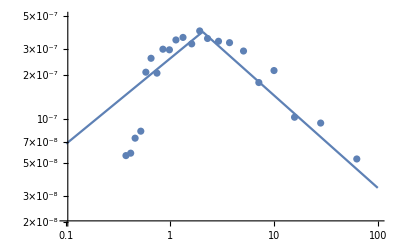

1.81217×10^-9

1.52914×10^-9

1.81217×10^-9

```mathematica
POINTS=Calore;
(*PointsErrors=ErrorCalore . {0,1};*)
PointsErrors=(CaloreYBars+Calore.{0,-1})

Eb=2.06 GeV;
n1=1.42;
n2=2.63;
GeV=1; (*GeV=0.00160218 erg*)

Clear[F1,F];
F[x_]=Piecewise[{{x^2 (x/Eb)^-n1,x<Eb},{x^2 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[POINTS,F0  F[x],F0,x,Weights->1/(PointsErrors.{1,1})^2,VarianceEstimatorFunction->(1&)]
(*F1[x_]=Fit[DiMauro,F[x],x]*)

Show[ListLogLogPlot[POINTS,PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}]]

NIntegrate[F1[x]/x,{x,0.1,100}] 0.00160218
NIntegrate[F1[x]/x,{x,0.1,10}] 0.00160218
```

FittedModel[Piecewise[{{2.38935×10^-7 x^0.394702, x<3.11054}, {(8.92166×10^-7)/x^0.766264, x>3.11054}, {0, True}}]]

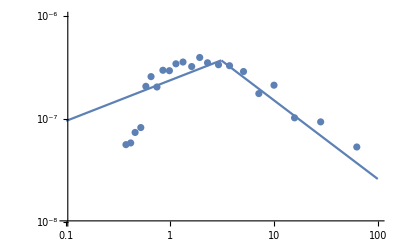

2.33931×10^-9

2.32569×10^-9

```mathematica
Clear[F0,n1,n2,Eb,POINTS];
POINTS=Calore;
PointsErrors=(CaloreYBars+Calore.{0,-1}).{1,1};

F[x_]=  Piecewise[{{F0 (x/Eb)^-n1,x<Eb},{F0 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[POINTS,{F[x],Eb>0},{F0,{n1,1.41},{n2,2.63},{Eb,2.06}},x,Weights->1/PointsErrors^2,VarianceEstimatorFunction->(1&)]
Show[ListLogLogPlot[POINTS,PlotRange->{{10^-1,10^2},{10^-8,10^-6}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{10^-8,10^-6}}]]
NIntegrate[F1[x]/x,{x,0.1,100}] 0.00160218
NIntegrate[F1[x]/x,{x,0.1,10}] 0.00160218
```

FittedModel[Piecewise[{{2.94163×10^-7 x^0.455388, x<2.06}, {(6.68131×10^-7)/x^0.679722, x>2.06}, {0, True}}]]

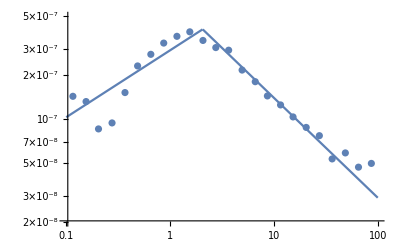

3.92597×10^-7 (Piecewise[{{0.743557 x^0.41, x<2.06}, {1.57665/x^0.63, x>2.06}, {0, True}}])

```mathematica
Clear[F0,n1,n2];
Eb=2.06;
F[x_]=Piecewise[{{x^2  F0 (x/Eb)^-n1,x<Eb},{x^2  F0 (x/Eb)^-n2,x>Eb}}];
F1=NonlinearModelFit[DiMauro,F[x],{F0,n1,n2},x]
Show[ListLogLogPlot[DiMauro,PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}],
LogLogPlot[F1[x],{x,10^-1,10^2},PlotRange->{{10^-1,10^2},{2 10^-8,5 10^-7}}]]
```

```mathematica
PointsErrors// MatrixForm
```

```mathematica
(*See the ROOT Results [Calore Method]*)
Clear[F0,n1,n2,Eb,POINTS];
Eb=2.06 GeV;
n1=1.42;
n2=2.63;
GeV=1; (*GeV=0.00160218 erg*)
F0=9.9377 10^-8;
F1[x_]=F0 Piecewise[{{x^2 (x/Eb)^-n1,x<Eb},{x^2 (x/Eb)^-n2,x>Eb}}];
NIntegrate[F1[x]/x,{x,0.1,100}] 0.00160218
NIntegrate[F1[x]/x,{x,0.1,10}] 0.00160218
```

1.94301×10^-9

1.63954×10^-9

```mathematica
(*See the ROOT Results [FreeFit Method]*)
Clear[F0,n1,n2,Eb,POINTS];
Eb=1.80840 GeV;
n1=-9.23923 10^-1;
n2=5.61343 10^-1;
GeV=1; (*GeV=0.00160218 erg*)
F0=4.41171 10^-7;
F1[x_]=F0 Piecewise[{{(x/Eb)^-n1,x<Eb},{ (x/Eb)^-n2,x>Eb}}];
NIntegrate[F1[x]/x,{x,0.1,100}] 0.00160218
NIntegrate[F1[x]/x,{x,0.1,10}] 0.00160218
```

1.83911×10^-9

1.48935×10^-9

```mathematica
(*Last Method*)
Clear[POINTS,F1];
POINTS=Calore;
F1=Interpolation[POINTS,InterpolationOrder->2];
NIntegrate[F1[x]/x,{x,0.35,62}] 0.00160218
NIntegrate[F1[x]/x,{x,0.35,10}] 0.00160218
```

1.71036×10^-9

1.40855×10^-9

```mathematica
(*REFERENCE 42*)
AIC={{-17.735173357664234,861.9931321988181},{-17.611724452554746,946.1719920451017},{-17.488275547445255,1093.595913336047},{-17.364826642335768,1246.6036979832309},{-17.24137773722628,1421.0191907949613},{-17.11792883211679,1609.6715456082065},{-16.9944799270073,1798.2883582829563},{-16.87103102189781,1996.3982946401766},{-16.747582116788323,2227.524114546515},{-16.62413321167883,2510.5702120151554},{-16.500684306569344,2953.3501849328604},{-16.377235401459856,3558.340554456744},{-16.253786496350365,4201.753871530058},{-16.130337591240878,4961.5081318750335},{-16.006888686131386,5684.242616636822},{-15.883439781021899,6302.511142187449},{-15.75999087591241,7175.271070886809},{-15.63654197080292,7875.979829777422},{-15.513093065693432,8623.373452056408},{-15.389644160583943,9429.810212192182},{-15.266195255474454,9805.168094822222},{-15.142746350364964,10131.480816454849},{-15.019297445255475,10234.05295131953},{-14.895848540145986,10169.824336545023},{-14.772399635036498,10017.315482652992},{-14.648950729927009,9585.43647991601},{-14.52550182481752,8932.823660868668},{-14.40205291970803,8097.204572430072},{-14.27860401459854,7211.501186915323},{-14.155155109489053,6398.4638705008765},{-14.031706204379564,5634.36158983417},{-13.913868613138687,4677.583167431803},{-13.781355277933747,3430.251833784642},{-13.65013686131387,2851.0404488270487},{-13.52668795620438,2235.0161142459992},{-13.396692518248177,1656.4484113770377},{-13.25734489051095,1204.7184622134164},{-13.14231295620438,897.1829285093002},{-13.055337591240876,684.2554323172905},{-12.963686131386863,514.2744259173232},{-12.879856502986067,353.3484599472582},{-12.800958029197082,254.02907040285777},{-12.71865875912409,195.36507726463154},{-12.647582116788323,134.792047506197},{-12.56154197080292,102.7935152385697},{-12.463032238442823,75.3251282910665},{-12.348312043795621,52.796971631975495},{-12.224863138686134,41.3833393505801},{-12.133679288321169,26.717931426867867},{-12.0827098540146,20.016830239781562},{-12.015,14.932495306500163},{-11.969236618004867,11.243834311418269},{-11.910629562043797,8.185178767528205},{-11.864336222627738,6.008798720500609},{-11.804014598540148,4.366525036351495}};

(*AICwErrors={{-17.778941605839417,623.4497391611966},{-17.75836678832117,889.623901060933},{-17.751824817518248,1110.1544690790593},{-17.651003649635037,678.1004211168172},{-17.635036496350367,1193.1150284921346},{-17.63491788321168,967.6367989722481},{-17.521943430656936,773.8191545838605},{-17.509224452554744,1110.838906906629},{-17.503649635036496,1329.3234711599416},{-17.39951476443265,911.0974655235195},{-17.37765250260688,1320.4564933544787},{-17.37226277372263,1650.1650571873286},{-17.272551703163018,1037.651590882174},{-17.253348540145986,1509.113698862136},{-17.24087591240876,1838.5512623869934},{-17.138971259124087,1152.8655401681463},{-17.129852874087593,1692.7362216498673},{-17.124087591240876,2048.444020615976},{-17.015678223844283,1281.8580671260631},{-17.00729927007299,2366.0390561145355},{-17.006403968978102,1894.4179158084116},{-16.883573958780595,2044.4126447223405},{-16.877443952033367,1400.7167568416226},{-16.875912408759127,2542.8504180966893},{-16.759124087591243,2833.147402976567},{-16.75824361313869,2137.2664375154045},{-16.745337591240876,1605.6230113897973},{-16.638161496350364,2367.3982507447517},{-16.627737226277375,3156.58528314097},{-16.60168795620438,1882.864439260431},{-16.525547445255476,3516.947490721351},{-16.52425182481752,2747.983491916943},{-16.51094890510949,2048.444020615976},{-16.432413321167886,3447.4064485388512},{-16.423357664233578,4211.270572221615},{-16.412306113138687,2458.174866107265},{-16.325330748175183,3986.8621328740855},{-16.32116788321168,4864.19474950843},{-16.284648722627736,2877.6391678058503},{-16.204379562043798,5824.494184289978},{-16.204379562043798,3156.58528314097},{-16.20301746611053,4213.74626574766},{-16.109618893879844,5286.73018723015},{-16.1021897810219,6489.430307986684},{-16.07703010948905,3822.5143943460716},{-15.99698636753972,5926.360642663167},{-15.985401459854016,7495.565124602608},{-15.949172314911367,4326.773961551464},{-15.87119691439947,6189.7849171152},{-15.854014598540147,8351.274111713074},{-15.854014598540147,4692.037801362983},{-15.754049484757408,7449.216641468032},{-15.751824817518251,9304.672580330143},{-15.731132690302399,5242.259312819943},{-15.635036496350367,10366.912960708527},{-15.634561507084587,8138.813164657029},{-15.607683785192911,5674.027077259201},{-15.518248175182483,11141.620375362701},{-15.509975669099756,8674.31518198032},{-15.475684306569343,6297.222826485339},{-15.391624624302276,9694.344685696668},{-15.386861313868614,11974.22077904795},{-15.354373044838376,6833.885980924348},{-15.266195255474454,10146.694376874211},{-15.255474452554747,12413.570458869755},{-15.252821949947863,7053.698463990942},{-15.142746350364964,10410.650592133758},{-15.138686131386862,12413.570458869755},{-15.128455748175183,7393.086746999728},{-15.017801094890512,10854.643016854596},{-15.007299270072995,13341.222221093207},{-15.004320907194995,7554.517654225282},{-14.892341468978103,10497.527611398444},{-14.890510948905112,13341.222221093207},{-14.880872002085505,7421.177804803303},{-14.768892563868615,10431.700166733232},{-14.765408302919708,7427.298666362505},{-14.759124087591243,12869.040447872536},{-14.645443658759126,9968.50570198903},{-14.64233576642336,12869.040447872536},{-14.636815693430655,7009.896655691183},{-14.524005474452556,9346.537577652642},{-14.516245023224949,6523.599677780638},{-14.51094890510949,11344.1793215166},{-14.380748175182482,5905.794956861959},{-14.38035583941606,8393.548769035522},{-14.379562043795621,9999.999999999989},{-14.258748596294218,7303.976169018824},{-14.257922749391728,5067.968909180209},{-14.248175182481752,8975.355166572359},{-14.148403284671534,4527.284684151354},{-14.13448253388947,6473.95679224987},{-14.13138686131387,7770.587123807769},{-14.032953163017032,4030.176572010303},{-14.032569483436273,5764.440638507576},{-14.029197080291974,7230.276894396076},{-13.916419210351693,4734.034723982487},{-13.912408759124089,5824.494184289978},{-13.903768248175185,3417.087527847205},{-13.791541970802921,2721.3587537584635},{-13.784808394160585,3761.1716248214343},{-13.781021897810222,4692.037801362983},{-13.647933043234142,2135.825675137287},{-13.635036496350367,3779.76490882236},{-13.632501303441085,2869.093702930154},{-13.514533368091767,1562.917977060525},{-13.507303417385534,2212.916968770989},{-13.503649635036497,2937.0992531515503},{-13.369045191069132,1140.1734148079677},{-13.36185561131387,1632.5529061177672},{-13.357664233576644,2048.444020615976},{-13.247525091240878,1460.0382163133263},{-13.246113968148645,839.8857153483657},{-13.240875912408761,1150.8874753884218},{-13.080291970802921,961.1376778706134},{-13.080291970802921,720.4270058188521},{-13.080291970802921,520.8886734271005},{-12.95492460622359,452.486983175274},{-12.948905109489054,326.06338620149677},{-12.943704379562043,581.2896705117141},{-12.86848083941606,321.35057782570664},{-12.86131386861314,227.40892841451094},{-12.86131386861314,419.61229055973547},{-12.735492700729928,249.24129424377816},{-12.73321167883212,204.3534317880945},{-12.729927007299272,142.3523471213787},{-12.585051703163018,98.21969791630141},{-12.583941605839417,137.31411429892975},{-12.583941605839417,176.71008909767232},{-12.48175182481752,57.82668886977605},{-12.48031152241919,80.22496527444493},{-12.478695255474452,110.37868219618754},{-12.385520072992703,54.31916079006106},{-12.384523266423358,37.94263980618774},{-12.382563868613138,75.86305379224967},{-12.280976277372265,48.443545341912554},{-12.277372262773724,59.94842503189396},{-12.277372262773724,32.48905573870442},{-12.208652676399028,28.586719908819415},{-12.205976277372264,42.496346165302455},{-12.204379562043798,51.901507071311734},{-12.129489051094891,19.220672715542012},{-12.1280370177268,26.98334592282258},{-12.124087591240878,34.91692529556037},{-12.065693430656937,10.44189550341823},{-12.05839416058394,17.293053078863938},{-12.056276068821687,23.77293955927567},{-11.987241484184917,7.232624177988733},{-11.985401459854018,11.845473504731306},{-11.985401459854018,15.803309434069243},{-11.927007299270075,4.477310508156859},{-11.927007299270075,7.687037477405681},{-11.91240875912409,11.021825252050114},{-11.824817518248178,6.899389153846851},{-11.824817518248178,4.988449398450599},{-11.824817518248178,2.703490716724295}};*)
AICwErrors={{10^-17.7789,623.45},{10^-17.7584,889.624},{10^-17.7518,1110.15},{10^-17.651,678.1},{10^-17.6349,967.637},{10^-17.635,1193.12},{10^-17.5219,773.819},{10^-17.5092,1110.84},{10^-17.5036,1329.32},{10^-17.3995,911.097},{10^-17.3777,1320.46},{10^-17.3723,1650.17},{10^-17.2726,1037.65},{10^-17.2533,1509.11},{10^-17.2409,1838.55},{10^-17.139,1152.87},{10^-17.1299,1692.74},{10^-17.1241,2048.44},{10^-17.0157,1281.86},{10^-17.0064,1894.42},{10^-17.0073,2366.04},{10^-16.8774,1400.72},{10^-16.8836,2044.41},{10^-16.8759,2542.85},{10^-16.7453,1605.62},{10^-16.7582,2137.27},{10^-16.7591,2833.15},{10^-16.6017,1882.86},{10^-16.6382,2367.4},{10^-16.6277,3156.59},{10^-16.5109,2048.44},{10^-16.5243,2747.98},{10^-16.5255,3516.95},{10^-16.4123,2458.17},{10^-16.4324,3447.41},{10^-16.4234,4211.27},{10^-16.2846,2877.64},{10^-16.3253,3986.86},{10^-16.3212,4864.19},{10^-16.2044,3156.59},{10^-16.203,4213.75},{10^-16.2044,5824.49},{10^-16.077,3822.51},{10^-16.1096,5286.73},{10^-16.1022,6489.43},{10^-15.9492,4326.77},{10^-15.997,5926.36},{10^-15.9854,7495.57},{10^-15.854,4692.04},{10^-15.8712,6189.78},{10^-15.854,8351.27},{10^-15.7311,5242.26},{10^-15.754,7449.22},{10^-15.7518,9304.67},{10^-15.6077,5674.03},{10^-15.6346,8138.81},{10^-15.635,10366.9},{10^-15.4757,6297.22},{10^-15.51,8674.32},{10^-15.5182,11141.6},{10^-15.3544,6833.89},{10^-15.3916,9694.34},{10^-15.3869,11974.2},{10^-15.2528,7053.7},{10^-15.2662,10146.7},{10^-15.2555,12413.6},{10^-15.1285,7393.09},{10^-15.1427,10410.7},{10^-15.1387,12413.6},{10^-15.0043,7554.52},{10^-15.0178,10854.6},{10^-15.0073,13341.2},{10^-14.8809,7421.18},{10^-14.8923,10497.5},{10^-14.8905,13341.2},{10^-14.7654,7427.3},{10^-14.7689,10431.7},{10^-14.7591,12869.},{10^-14.6368,7009.9},{10^-14.6454,9968.51},{10^-14.6423,12869.},{10^-14.5162,6523.6},{10^-14.524,9346.54},{10^-14.5109,11344.2},{10^-14.3807,5905.79},{10^-14.3804,8393.55},{10^-14.3796,10000.},{10^-14.2579,5067.97},{10^-14.2587,7303.98},{10^-14.2482,8975.36},{10^-14.1484,4527.28},{10^-14.1345,6473.96},{10^-14.1314,7770.59},{10^-14.033,4030.18},{10^-14.0326,5764.44},{10^-14.0292,7230.28},{10^-13.9038,3417.09},{10^-13.9164,4734.03},{10^-13.9124,5824.49},{10^-13.7915,2721.36},{10^-13.7848,3761.17},{10^-13.781,4692.04},{10^-13.6479,2135.83},{10^-13.6325,2869.09},{10^-13.635,3779.76},{10^-13.5145,1562.92},{10^-13.5073,2212.92},{10^-13.5036,2937.1},{10^-13.369,1140.17},{10^-13.3619,1632.55},{10^-13.3577,2048.44},{10^-13.2461,839.886},{10^-13.2409,1150.89},{10^-13.2475,1460.04},{10^-13.0803,520.889},{10^-13.0803,720.427},{10^-13.0803,961.138},{10^-12.9489,326.063},{10^-12.9549,452.487},{10^-12.9437,581.29},{10^-12.8613,227.409},{10^-12.8685,321.351},{10^-12.8613,419.612},{10^-12.7299,142.352},{10^-12.7332,204.353},{10^-12.7355,249.241},{10^-12.5851,98.2197},{10^-12.5839,137.314},{10^-12.5839,176.71},{10^-12.4818,57.8267},{10^-12.4803,80.225},{10^-12.4787,110.379},{10^-12.3845,37.9426},{10^-12.3855,54.3192},{10^-12.3826,75.8631},{10^-12.2774,32.4891},{10^-12.281,48.4435},{10^-12.2774,59.9484},{10^-12.2087,28.5867},{10^-12.206,42.4963},{10^-12.2044,51.9015},{10^-12.1295,19.2207},{10^-12.128,26.9833},{10^-12.1241,34.9169},{10^-12.0657,10.4419},{10^-12.0584,17.2931},{10^-12.0563,23.7729},{10^-11.9872,7.23262},{10^-11.9854,11.8455},{10^-11.9854,15.8033},{10^-11.927,4.47731},{10^-11.927,7.68704},{10^-11.9124,11.0218},{10^-11.8248,2.70349},{10^-11.8248,4.98845},{10^-11.8248,6.89939}};
AIC={};
AICHErr={};
AICLErr={};
For[i=1,i<53,i++,
If[AICwErrors[[i*3-2]].{0,1}>AICwErrors[[i*3-1]].{0,1},AICwErrors[[{i*3-2,i*3-1}]]=AICwErrors[[{i*3-1,i*3-2}]] ];
If[AICwErrors[[i*3-1]].{0,1}>AICwErrors[[i*3]].{0,1},AICwErrors[[{i*3-1,i*3}]]=AICwErrors[[{i*3,i*3-1}]] ];
If[AICwErrors[[i*3-2]].{0,1}>AICwErrors[[i*3-1]].{0,1},AICwErrors[[{i*3-2,i*3-1}]]=AICwErrors[[{i*3-1,i*3-2}]] ];
]

For[i=1,i<53,i++,AppendTo[AICHErr,AICwErrors[[i*3]]]]
For[i=1,i<53,i++,AppendTo[AIC,AICwErrors[[i*3-1]]]]
For[i=1,i<53,i++,AppendTo[AICLErr,AICwErrors[[i*3-2]]]]
```

```mathematica
AICH=AICHErr.{0,1}-AIC.{0,1};
AICL=AICLErr.{0,1}-AIC.{0,1};

For[i=1,i<53,i++,
AppendTo[AIC[[i]],0];
AppendTo[AIC[[i]],0];
AppendTo[AIC[[i]],AICL[[i]]];
AppendTo[AIC[[i]],AICH[[i]]]
]


AIC.DiagonalMatrix[{4 Pi R0^2,1/( 5*10^33), 1, 1,1/( 5 10^33),1/( 5*10^33)}]//MatrixForm
```

(1.50813×10^28 | 1.77925×10^-31 | 0. | 0. | -5.32348×10^-32 | 4.41052×10^-32
2.00419×10^28 | 1.93527×10^-31 | 0. | 0. | -5.79074×10^-32 | 4.50966×10^-32
2.67695×10^28 | 2.22168×10^-31 | 0. | 0. | -6.74042×10^-32 | 4.3696×10^-32
3.62359×10^28 | 2.64092×10^-31 | 0. | 0. | -8.18726×10^-32 | 6.5942×10^-32
4.82547×10^28 | 3.01822×10^-31 | 0. | 0. | -9.4292×10^-32 | 6.5888×10^-32
6.4112×10^28 | 3.38548×10^-31 | 0. | 0. | -1.07974×10^-31 | 7.114×10^-32
8.52×10^28 | 3.78884×10^-31 | 0. | 0. | -1.22512×10^-31 | 9.4324×10^-32
1.13042×10^29 | 4.08882×10^-31 | 0. | 0. | -1.28738×10^-31 | 9.9688×10^-32
1.50883×10^29 | 4.27454×10^-31 | 0. | 0. | -1.0633×10^-31 | 1.39176×10^-31
1.98902×10^29 | 4.7348×10^-31 | 0. | 0. | -9.6908×10^-32 | 1.57838×10^-31
2.58547×10^29 | 5.49596×10^-31 | 0. | 0. | -1.39908×10^-31 | 1.53794×10^-31
3.19477×10^29 | 6.89482×10^-31 | 0. | 0. | -1.97848×10^-31 | 1.52772×10^-31
4.08827×10^29 | 7.97372×10^-31 | 0. | 0. | -2.21844×10^-31 | 1.75466×10^-31
5.41801×10^29 | 8.4275×10^-31 | 0. | 0. | -2.11432×10^-31 | 3.22148×10^-31
6.71799×10^29 | 1.05735×10^-30 | 0. | 0. | -2.92844×10^-31 | 2.4054×10^-31
8.70642×10^29 | 1.18527×10^-30 | 0. | 0. | -3.19918×10^-31 | 3.13842×10^-31
1.16316×10^30 | 1.23796×10^-30 | 0. | 0. | -2.99548×10^-31 | 4.32298×10^-31
1.52349×10^30 | 1.48984×10^-30 | 0. | 0. | -4.41392×10^-31 | 3.7109×10^-31
2.00558×10^30 | 1.62776×10^-30 | 0. | 0. | -4.92956×10^-31 | 4.45618×10^-31
2.67202×10^30 | 1.73486×10^-30 | 0. | 0. | -4.7542×10^-31 | 4.93456×10^-31
3.50945×10^30 | 1.93887×10^-30 | 0. | 0. | -5.7209×10^-31 | 4.55972×10^-31
4.68424×10^30 | 2.02934×10^-30 | 0. | 0. | -6.186×10^-31 | 4.5338×10^-31
6.225×10^30 | 2.08214×10^-30 | 0. | 0. | -6.03522×10^-31 | 4.0058×10^-31
8.29926×10^30 | 2.17092×10^-30 | 0. | 0. | -6.60016×10^-31 | 4.9732×10^-31
1.108×10^31 | 2.0995×10^-30 | 0. | 0. | -6.15264×10^-31 | 5.6874×10^-31
1.47211×10^31 | 2.08634×10^-30 | 0. | 0. | -6.0088×10^-31 | 4.8746×10^-31
1.95632×10^31 | 1.9937×10^-30 | 0. | 0. | -5.91722×10^-31 | 5.80098×10^-31
2.58726×10^31 | 1.86931×10^-30 | 0. | 0. | -5.64588×10^-31 | 3.99532×10^-31
3.60114×10^31 | 1.67871×10^-30 | 0. | 0. | -4.97552×10^-31 | 3.2129×10^-31
4.76584×10^31 | 1.4608×10^-30 | 0. | 0. | -4.47202×10^-31 | 3.34276×10^-31
6.34366×10^31 | 1.29479×10^-30 | 0. | 0. | -3.89336×10^-31 | 2.59326×10^-31
8.0212×10^31 | 1.15289×10^-30 | 0. | 0. | -3.46852×10^-31 | 2.93168×10^-31
1.04819×10^32 | 9.46806×10^-31 | 0. | 0. | -2.63388×10^-31 | 2.18092×10^-31
1.41919×10^32 | 7.52234×10^-31 | 0. | 0. | -2.07962×10^-31 | 1.86174×10^-31
2.0153×10^32 | 5.73818×10^-31 | 0. | 0. | -1.46652×10^-31 | 1.82134×10^-31
2.68868×10^32 | 4.42584×10^-31 | 0. | 0. | -1.3×10^-31 | 1.44836×10^-31
3.75785×10^32 | 3.2651×10^-31 | 0. | 0. | -9.8476×10^-32 | 8.3178×10^-32
4.96523×10^32 | 2.30178×10^-31 | 0. | 0. | -6.22008×10^-32 | 6.183×10^-32
7.18687×10^32 | 1.44085×10^-31 | 0. | 0. | -3.99076×10^-32 | 4.81422×10^-32
9.59267×10^32 | 9.04974×10^-32 | 0. | 0. | -2.52848×10^-32 | 2.57606×10^-32
1.17041×10^33 | 6.42702×10^-32 | 0. | 0. | -1.87884×10^-32 | 1.96522×10^-32
1.59823×10^33 | 4.08706×10^-32 | 0. | 0. | -1.24002×10^-32 | 8.9776×10^-33
2.25393×10^33 | 2.74628×10^-32 | 0. | 0. | -7.81886×10^-33 | 7.8792×10^-33
2.86114×10^33 | 1.6045×10^-32 | 0. | 0. | -4.47966×10^-33 | 6.0308×10^-33
3.55909×10^33 | 1.08638×10^-32 | 0. | 0. | -3.27532×10^-33 | 4.30878×10^-33
4.5273×10^33 | 9.6887×10^-33 | 0. | 0. | -3.19088×10^-33 | 2.30098×10^-33
5.38071×10^33 | 8.49926×10^-33 | 0. | 0. | -2.78192×10^-33 | 1.88104×10^-33
6.43931×10^33 | 5.39666×10^-33 | 0. | 0. | -1.55252×10^-33 | 1.58672×10^-33
7.55857×10^33 | 3.45862×10^-33 | 0. | 0. | -1.37024×10^-33 | 1.29596×10^-33
8.9421×10^33 | 2.3691×10^-33 | 0. | 0. | -9.22576×10^-34 | 7.9156×10^-34
1.02292×10^34 | 1.53741×10^-33 | 0. | 0. | -6.41946×10^-34 | 6.66952×10^-34
1.29431×10^34 | 9.9769×10^-34 | 0. | 0. | -4.56992×10^-34 | 3.82188×10^-34)

```mathematica
(*Converting Flux to Luminosity*)
Clear[kpc,cm,R0,rc,ρ,rLat];
R0=8.5 kpc; (*If we assume all MSPs are in the galactic center*)
rc=20 kpc;
kpc=3.086 10^21 cm;
cm=1;
1/(4 Pi R0^2)

ρ[r_]:=(r/rc)^(-2γ)(1+r/rc)^(-6+2 γ);
γ=1;
rLat[s_,b_,l_]=R0^2+s^2-2 R0 s Cos[b] Cos[l];
NIntegrate[ρ[rLat[s,b,l]] Sin[b],{s,0,Infinity},{b,2 Degree,20 Degree},{l,-20  Degree,20 Degree},Method->"Trapezoidal"]/(4 Pi NIntegrate[s^2 ρ[rLat[s,b,l]] Sin[b],{s,0,Infinity},{b,2 Degree,20 Degree},{l,-20  Degree,20 Degree},Method->"Trapezoidal"])
```

1.15654×10^-46

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in b in the region {{0.,∞},{0.0349066,0.349066},{0.,0.349066}}. NIntegrate obtained 2.25823×10^-99 and 6.57633×10^-99 for the integral and error estimates.

NIntegrate::ncvi: NIntegrate failed to converge to prescribed accuracy after 9 iterated refinements in b in the region {{0.,∞},{0.0349066,0.349066},{0.,0.349066}}. NIntegrate obtained 1.52609×10^-54 and 4.4413×10^-54 for the integral and error estimates.

1.17755×10^-46

```mathematica
(*Here we Get AIC Datas and we Normalize them*)
Clear[Normalization];
Normalization=NIntegrate[Interpolation[AIC.DiagonalMatrix[{4 Pi R0^2,1}]][x],{x,1.6 10^28,10^34},Method->"GlobalAdaptive",MinRecursion->5];
```

```mathematica
AICH=AICHErr.{0,1}-AIC.{0,1};
AICL=AICLErr.{0,1}-AIC.{0,1};

For[i=1,i<53,i++,
AppendTo[AIC[[i]],0];
AppendTo[AIC[[i]],0];
AppendTo[AIC[[i]],AICL[[i]]];
AppendTo[AIC[[i]],AICH[[i]]]
]


AIC.DiagonalMatrix[{4 Pi R0^2,1/Normalization, 1, 1,1/Normalization,1/Normalization}]//MatrixForm
```

(1.50813×10^28 | 3.43749×10^-34 | 0. | 0. | -1.02849×10^-34 | 8.52108×10^-35
2.00419×10^28 | 3.73893×10^-34 | 0. | 0. | -1.11876×10^-34 | 8.71261×10^-35
2.67695×10^28 | 4.29226×10^-34 | 0. | 0. | -1.30224×10^-34 | 8.44202×10^-35
3.62359×10^28 | 5.10223×10^-34 | 0. | 0. | -1.58177×10^-34 | 1.27399×10^-34
4.82547×10^28 | 5.83117×10^-34 | 0. | 0. | -1.82171×10^-34 | 1.27295×10^-34
6.4112×10^28 | 6.54071×10^-34 | 0. | 0. | -2.08605×10^-34 | 1.37442×10^-34
8.52×10^28 | 7.32×10^-34 | 0. | 0. | -2.36692×10^-34 | 1.82233×10^-34
1.13042×10^29 | 7.89955×10^-34 | 0. | 0. | -2.4872×10^-34 | 1.92596×10^-34
1.50883×10^29 | 8.25836×10^-34 | 0. | 0. | -2.05428×10^-34 | 2.68886×10^-34
1.98902×10^29 | 9.14758×10^-34 | 0. | 0. | -1.87225×10^-34 | 3.04941×10^-34
2.58547×10^29 | 1.06181×10^-33 | 0. | 0. | -2.70301×10^-34 | 2.97128×10^-34
3.19477×10^29 | 1.33207×10^-33 | 0. | 0. | -3.8224×10^-34 | 2.95154×10^-34
4.08827×10^29 | 1.54051×10^-33 | 0. | 0. | -4.286×10^-34 | 3.38998×10^-34
5.41801×10^29 | 1.62818×10^-33 | 0. | 0. | -4.08484×10^-34 | 6.22386×10^-34
6.71799×10^29 | 2.04278×10^-33 | 0. | 0. | -5.65771×10^-34 | 4.64721×10^-34
8.70642×10^29 | 2.28993×10^-33 | 0. | 0. | -6.18078×10^-34 | 6.06339×10^-34
1.16316×10^30 | 2.39172×10^-33 | 0. | 0. | -5.78723×10^-34 | 8.35195×10^-34
1.52349×10^30 | 2.87836×10^-33 | 0. | 0. | -8.52764×10^-34 | 7.16942×10^-34
2.00558×10^30 | 3.14482×10^-33 | 0. | 0. | -9.52385×10^-34 | 8.60929×10^-34
2.67202×10^30 | 3.35174×10^-33 | 0. | 0. | -9.18506×10^-34 | 9.53351×10^-34
3.50945×10^30 | 3.74587×10^-33 | 0. | 0. | -1.10527×10^-33 | 8.80933×10^-34
4.68424×10^30 | 3.92066×10^-33 | 0. | 0. | -1.19513×10^-33 | 8.75925×10^-34
6.225×10^30 | 4.02267×10^-33 | 0. | 0. | -1.166×10^-33 | 7.73916×10^-34
8.29926×10^30 | 4.19419×10^-33 | 0. | 0. | -1.27514×10^-33 | 9.60817×10^-34
1.108×10^31 | 4.05621×10^-33 | 0. | 0. | -1.18868×10^-33 | 1.0988×10^-33
1.47211×10^31 | 4.03079×10^-33 | 0. | 0. | -1.16089×10^-33 | 9.41767×10^-34
1.95632×10^31 | 3.85181×10^-33 | 0. | 0. | -1.1432×10^-33 | 1.12074×10^-33
2.58726×10^31 | 3.61148×10^-33 | 0. | 0. | -1.09078×10^-33 | 7.71891×10^-34
3.60114×10^31 | 3.24325×10^-33 | 0. | 0. | -9.61265×10^-34 | 6.20729×10^-34
4.76584×10^31 | 2.82224×10^-33 | 0. | 0. | -8.63989×10^-34 | 6.45817×10^-34
6.34366×10^31 | 2.50152×10^-33 | 0. | 0. | -7.52193×10^-34 | 5.01015×10^-34
8.0212×10^31 | 2.22737×10^-33 | 0. | 0. | -6.70114×10^-34 | 5.66397×10^-34
1.04819×10^32 | 1.82922×10^-33 | 0. | 0. | -5.08863×10^-34 | 4.21351×10^-34
1.41919×10^32 | 1.45331×10^-33 | 0. | 0. | -4.0178×10^-34 | 3.59686×10^-34
2.0153×10^32 | 1.10861×10^-33 | 0. | 0. | -2.8333×10^-34 | 3.51881×10^-34
2.68868×10^32 | 8.55067×10^-34 | 0. | 0. | -2.51159×10^-34 | 2.79822×10^-34
3.75785×10^32 | 6.30814×10^-34 | 0. | 0. | -1.90255×10^-34 | 1.60699×10^-34
4.96523×10^32 | 4.44701×10^-34 | 0. | 0. | -1.20171×10^-34 | 1.19455×10^-34
7.18687×10^32 | 2.78371×10^-34 | 0. | 0. | -7.7101×10^-35 | 9.30102×10^-35
9.59267×10^32 | 1.7484×10^-34 | 0. | 0. | -4.88499×10^-35 | 4.97692×10^-35
1.17041×10^33 | 1.24169×10^-34 | 0. | 0. | -3.6299×10^-35 | 3.79678×10^-35
1.59823×10^33 | 7.89615×10^-35 | 0. | 0. | -2.3957×10^-35 | 1.73446×10^-35
2.25393×10^33 | 5.30578×10^-35 | 0. | 0. | -1.51059×10^-35 | 1.52225×10^-35
2.86114×10^33 | 3.09988×10^-35 | 0. | 0. | -8.65465×10^-36 | 1.16514×10^-35
3.55909×10^33 | 2.09888×10^-35 | 0. | 0. | -6.32788×10^-36 | 8.32451×10^-36
4.5273×10^33 | 1.87185×10^-35 | 0. | 0. | -6.16474×10^-36 | 4.44547×10^-36
5.38071×10^33 | 1.64205×10^-35 | 0. | 0. | -5.37464×10^-36 | 3.63415×10^-36
6.43931×10^33 | 1.04263×10^-35 | 0. | 0. | -2.99945×10^-36 | 3.06553×10^-36
7.55857×10^33 | 6.68202×10^-36 | 0. | 0. | -2.64729×10^-36 | 2.50378×10^-36
8.9421×10^33 | 4.57707×10^-36 | 0. | 0. | -1.78241×10^-36 | 1.52929×10^-36
1.02292×10^34 | 2.97026×10^-36 | 0. | 0. | -1.24023×10^-36 | 1.28854×10^-36
1.29431×10^34 | 1.92753×10^-36 | 0. | 0. | -8.82903×10^-37 | 7.38383×10^-37)

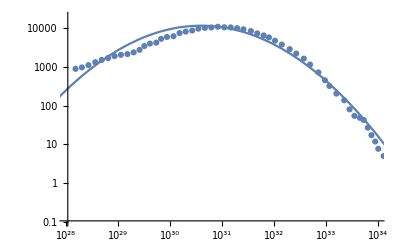

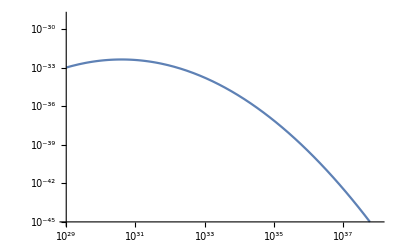

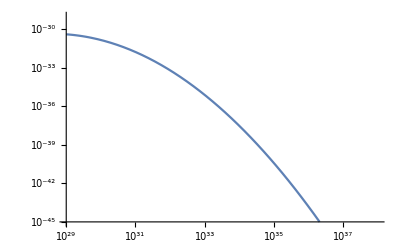

FittedModel::constr: The property values {ParameterTable} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

| Estimate | Standard Error | t-Statistic | P-Value
L0 | 2.12364×10^28 | 2.68914×10^61 | 7.89712×10^-34 | 1

```mathematica
(*Using Log Normal and the values extracted from page 15 we DON'T simulate the expected curve*)
Clear[L0,σ];
F[x_]:=  E^(-(Log10[x]-Log10[L0])^2/(2σ^2))   Log10[E]/(σ Sqrt[2 Pi] x);

(*MY ROOT VALUES*)
(*L0=3.65649 10^32; 
σ=0.882369;*)
L0=4.3 10^32;  (*THERE WAS A MISTAKE HERE*)
σ=0.94;


Show[ListLogLogPlot[AIC.DiagonalMatrix[{4 Pi R0^2,1}],PlotRange->{{10^28,10^34},{10^-1,2 10^4}}],
	LogLogPlot[Normalization  F[x],{x,10^27,10^36}]]
LogLogPlot[F[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-45,10^-29}}]
L0=4.3 10^30; 
σ=0.94;
LogLogPlot[F[x],{x,10^29,10^38},PlotRange->{{10^29,10^38},{10^-45,10^-29}}]
(*F1=NonlinearModelFit[AIC,{F[x],L0>0,σ>0},{L0,σ},x,Tolerance->10^(-12)];
F1["ParameterTable"]*)
```

```mathematica
0
```

General::munfl: Exp[-2956.41] is too small to represent as a normalized machine number; precision may be lost.

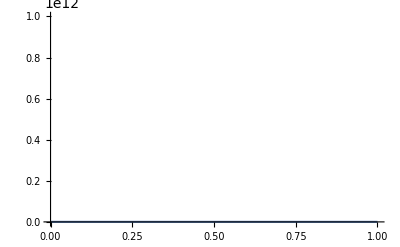

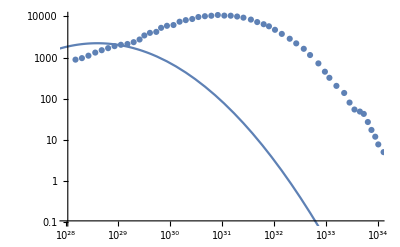

```mathematica
Clear[L0,σ]
F[x_]= E^(-(Log10[x]-Log10[L0])^2/(2σ^2))   Log10[E]/(σ  √(2 π)  x);
L0= 1.42 10^30;
σ=0.6089;
Plot[F[x],{x,10^-18,10^-12},PlotRange->{{10^-18,10^-12},{0,10^12}}]
```

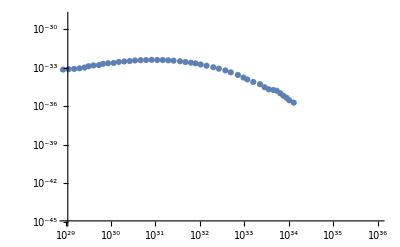

InterpolatingFunction::dmvali: The integration endpoint 10000000000000000000000000000 in dimension 1 lies outside the range of data in the interpolating function. Extrapolation will be used.

2.58801×10^36

```mathematica
ListLogLogPlot[AIC.DiagonalMatrix[{4 Pi R0^2,1/Normalization}],PlotRange->{{10^29,10^36},{10^-45,10^-29}}]
```